```mathematica
Numerical evoluation of Subscript[p, 0,s] coefficients (without the overall factor of 2πω)
f[e_,s_]:=NIntegrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π}]
```

2 coefficients evoluation factor Numerical of^2 overall the without πω p_(0,s)

```mathematica
Analytical expression of Subscript[p, 0,s] coefficients (without the overall factor of 2πω)
g[e_,s_]:=Integrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π}]
```

2 Analytical coefficients expression factor of^2 overall the without πω p_(0,s)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

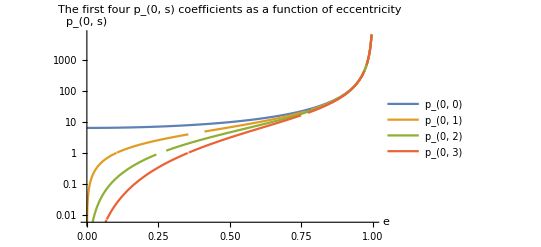

```mathematica
LogPlot[{f[e, 0],f[e,1], f[e, 2], f[e, 3]}, {e, 0, 1}, PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)"},PlotLabel->Style["The first four p_(0, s) coefficients as a function of eccentricity",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)",FontSize->24]}]
```

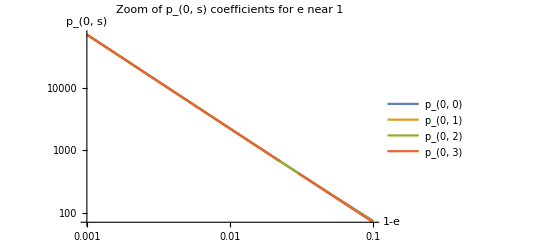

```mathematica
LogLogPlot[{f[1-x, 0],f[1-x,1],f[1-x,2],f[1-x,3]},{x,10^-3,10^-1},PlotPoints->100,PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)"},PlotLabel->Style["Zoom of p_(0, s) coefficients for e near 1",FontSize->32],AxesLabel->{Style["1-e",FontSize->24],Style["p_(0, s)",FontSize->24]}]
```

```mathematica
The above look very linear, so check if the slope appears to be constant for e->1
Limit[D[Log[g[1-Exp[-x],0]],x],x->Infinity]
```

3/2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

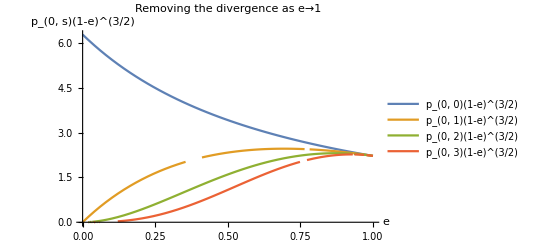

```mathematica
Plot[{f[e,0]*(1-e)^1.5,f[e,1]*(1-e)^1.5,f[e,2]*(1-e)^1.5,f[e,3]*(1-e)^1.5},{e,0,1},PlotLegends->{"p_(0, 0)(1-e)^(3/2)","p_(0, 1)(1-e)^(3/2)","p_(0, 2)(1-e)^(3/2)","p_(0, 3)(1-e)^(3/2)"},PlotLabel->Style["Removing the divergence as e→1",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)(1-e)^(3/2)",FontSize->24]}]
```

```mathematica
Limit[g[1-x,0]*x^(3/2),x->0]
```

Indeterminate

```mathematica
f[e,0]*(1-e)^(3/2)/.e->0.9999
```

NIntegrate::inumr: The integrand 1/(1-e Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

2.22161